```mathematica
pdiff[V1_,V2_,precision_]:=
Module[{x1,x2,x3,y1,y2,diff,x1start,x1end,x1new,area},
y1 =a/.FindRoot[Integrate[density[x],{x,0,a}]==V1/2,{a,0}];
y2=a/.FindRoot[Integrate[density[x],{x,y1,a}]==V2/2,{a,y1}];

x1start=-y2;
x1end=-y1;
While[x1end-x1start>precision,
x1new = (x1start+x1end)/2;
x2=a/.FindRoot[Integrate[density[x],{x,x1new,a}]==V1,{a,x1new/2}];
x3=Solve[]
area=NIntegrate[density[x],{x,x2,-(x1new+x2)}];
If[area>V2,x1start=x1new,x1end=x1new]
];
x1=(x1start+x1end)/2;

x2=a/.FindRoot[Integrate[density[x],{x,x1,a}]==V1,{a,x1/2}];
x3=-(x1+x2);
diff=2density[y1]+2 density[y2]-density[x1]-density[x2]-density[x3];
Return[diff];
]
```

```mathematica
table[range_,blocks_,precision_]:=
Module[{g},
g=Table[0,{i,blocks},{j,blocks}];
For[i=1,i≤blocks,i++,
For[j=i,j≤blocks,j++,
g[[i,j]]=pdiff[i*range/blocks,j*range/blocks,precision];
]
];
Return[g];
]
```

```mathematica
g=table[0, ];
```

$Aborted

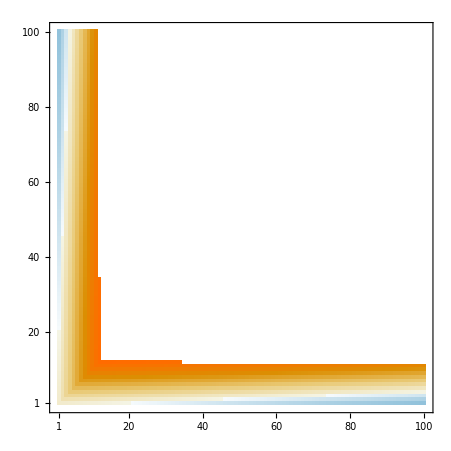

```mathematica
MatrixPlot[g+Transpose[g]-IdentityMatrix[100]*Diagonal[g], DataReversed->True]
```

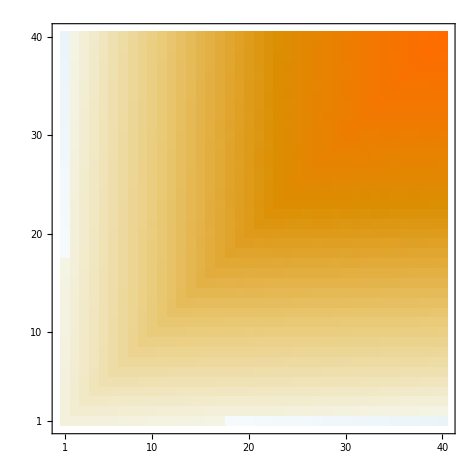

```mathematica
MatrixPlot[h1+Transpose[h1]-IdentityMatrix[40]*Diagonal[h1], DataReversed->True]
```

```mathematica
MatrixPlot[h+Transpose[h]-IdentityMatrix[100]*Diagonal[h], DataReversed->True, PlotLegends->Automatic, Frame->False]
```

```mathematica
pdiff[2, 2, 0.0001]
```

2.76576

```mathematica
boundary[v1range_,v1block_,v2block_,precision_]:=
Module[{v2=0, list={}},
While[pdiff[0, v2, precision]>0,
v2+= v2block;
];
AppendTo[list, {v2-v2block/2,0}];
For[v1=v1block,v1≤v1range,v1+=v1block,
While[pdiff[v1,v2,precision]>0,
Print["v1=",v1," v2=",v2];
v2+=v2block
];
AppendTo[list, {v2-v2block/2,v1}];
];
Return[list];
];
```

```mathematica
a=boundary[10, 0.1, 0.1, 0.00001]
```

```mathematica
a
```

{{3.15,0},{3.35,0.1},{3.55,0.2},{3.85,0.3},{4.05,0.4},{4.45,0.5},{4.75,0.6},{5.15,0.7},{5.55,0.8},{5.95,0.9},{6.35,1.},{6.85,1.1},{7.35,1.2},{7.95,1.3},{8.55,1.4},{9.15,1.5},{9.75,1.6},{10.35,1.7},{11.05,1.8},{11.75,1.9},{12.45,2.},{13.15,2.1},{13.95,2.2},{14.65,2.3},{15.45,2.4},{16.25,2.5},{17.15,2.6},{17.95,2.7},{18.85,2.8},{19.65,2.9},{20.65,3.},{21.55,3.1},{22.45,3.2},{23.45,3.3},{24.35,3.4},{25.35,3.5},{26.35,3.6},{27.35,3.7},{28.35,3.8},{29.35,3.9},{30.45,4.},{31.45,4.1},{32.55,4.2},{33.55,4.3},{34.65,4.4},{35.85,4.5},{36.85,4.6},{37.95,4.7},{39.05,4.8},{40.35,4.9},{41.35,5.},{42.55,5.1},{43.85,5.2},{44.85,5.3},{45.95,5.4},{47.15,5.5},{48.35,5.6},{49.75,5.7},{50.75,5.8},{52.15,5.9},{53.45,6.},{54.65,6.1},{55.85,6.2},{56.95,6.3},{58.15,6.4},{59.65,6.5},{60.85,6.6},{61.95,6.7},{63.35,6.8},{64.85,6.9},{66.15,7.},{67.45,7.1},{68.65,7.2},{69.95,7.3},{71.55,7.4},{72.55,7.5},{73.95,7.6},{75.35,7.7},{76.65,7.8},{77.85,7.9},{79.45,8.},{81.05,8.1},{82.05,8.2},{83.65,8.3},{84.95,8.4},{86.35,8.5},{88.05,8.6},{89.35,8.7},{90.25,8.8},{92.15,8.9},{93.15,9.},{94.45,9.1},{96.05,9.2},{97.75,9.3},{98.65,9.4},{100.35,9.5},{101.85,9.6},{103.65,9.7},{105.05,9.8},{106.05,9.9},{107.55,10.}}

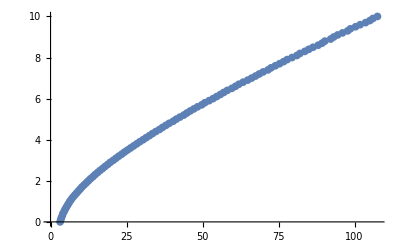

```mathematica
ListPlot[a]
```

```mathematica
f=Interpolation[a, InterpolationOrder->1]
```

InterpolatingFunction[{{3.15, 107.55}}, <>]

InterpolatingFunction::dmval: Input value {0.00224714} lies outside the range of data in the interpolating function. Extrapolation will be used.

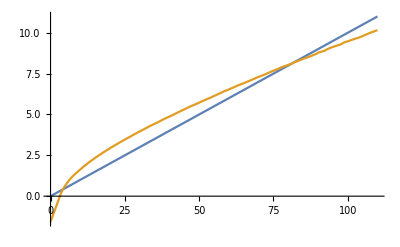

```mathematica
Plot[{0.1*x, f[x]}, {x, 0, 110}]
```

```mathematica
pdiff[100, 1000, 0.000000001]
```

233.745

```mathematica
For[i=1, i≤ Length[a], i++, a[[i, 1]]=a[[i, 1]]^2]
```

```mathematica
a
```

{{3.15,0},{3.35,0.1},{3.55,0.2},{3.85,0.3},{4.05,0.4},{4.45,0.5},{4.75,0.6},{5.15,0.7},{5.55,0.8},{5.95,0.9},{6.35,1.},{6.85,1.1},{7.35,1.2},{7.95,1.3},{8.55,1.4},{9.15,1.5},{9.75,1.6},{10.35,1.7},{11.05,1.8},{11.75,1.9},{12.45,2.},{13.15,2.1},{13.95,2.2},{14.65,2.3},{15.45,2.4},{16.25,2.5},{17.15,2.6},{17.95,2.7},{18.85,2.8},{19.65,2.9},{20.65,3.},{21.55,3.1},{22.45,3.2},{23.45,3.3},{24.35,3.4},{25.35,3.5},{26.35,3.6},{27.35,3.7},{28.35,3.8},{29.35,3.9},{30.45,4.},{31.45,4.1},{32.55,4.2},{33.55,4.3},{34.65,4.4},{35.85,4.5},{36.85,4.6},{37.95,4.7},{39.05,4.8},{40.35,4.9},{41.35,5.},{42.55,5.1},{43.85,5.2},{44.85,5.3},{45.95,5.4},{47.15,5.5},{48.35,5.6},{49.75,5.7},{50.75,5.8},{52.15,5.9},{53.45,6.},{54.65,6.1},{55.85,6.2},{56.95,6.3},{58.15,6.4},{59.65,6.5},{60.85,6.6},{61.95,6.7},{63.35,6.8},{64.85,6.9},{66.15,7.},{67.45,7.1},{68.65,7.2},{69.95,7.3},{71.55,7.4},{72.55,7.5},{73.95,7.6},{75.35,7.7},{76.65,7.8},{77.85,7.9},{79.45,8.},{81.05,8.1},{82.05,8.2},{83.65,8.3},{84.95,8.4},{86.35,8.5},{88.05,8.6},{89.35,8.7},{90.25,8.8},{92.15,8.9},{93.15,9.},{94.45,9.1},{96.05,9.2},{97.75,9.3},{98.65,9.4},{100.35,9.5},{101.85,9.6},{103.65,9.7},{105.05,9.8},{106.05,9.9},{107.55,10.}}

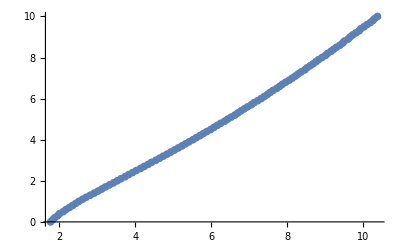

```mathematica
ListPlot[a]
```

```mathematica
lm=LinearModelFit[a, x, x]
```

FittedModel[-2.04235+1.12518 x]

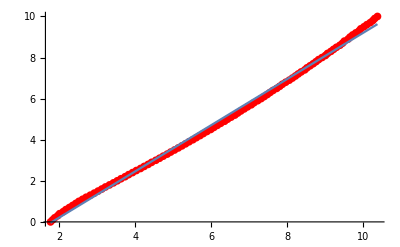

```mathematica
Show[ListPlot[a,PlotStyle->Red],Plot[%471[x],{x,1.7748239349298853,10.370631610466074}]]
```

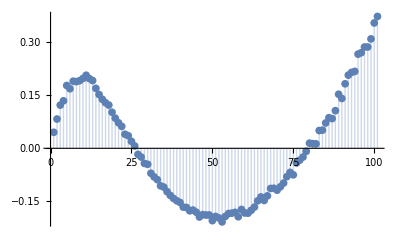

```mathematica
ListPlot[lm["FitResiduals"], Filling->Axis]
```

Alternate calculations

```mathematica
density[x_]:=Evaluate[Normal[Series[E^(x^(2)),{x, 0, 50}]]];
(*density[x_]:=Evaluate[den[Abs[x]]];*)
psix[x_]:=(2)x^(1);
```

```mathematica
getdiff[V1_,y1_,x1_]:=
Module[{x2,x3,p2,V2,y2,p3},
x2=a/.FindRoot[Integrate[density[x],{x,x1,a}]==V1,{a,x1/2}];
x3=a/.FindRoot[psix[x1]+psix[x2]+psix[a]==0,{a, -x1}];
p2=density[x1]+density[x2]+density[x3];
V2=NIntegrate[density[x],{x,x2,x3}];
y2=a/.FindRoot[Integrate[density[x],{x,y1,a}]==V2/2,{a,y1}];
p3=2 density[y1]+2 density[y2];
Return[{p3-p2,V2}];
]
```

```mathematica
getV2[V1_,precision_]:=
Module[{y1,x1start,x1end,x1,diff},
y1 =a/.FindRoot[Integrate[density[x],{x,0,a}]==V1/2,{a,0}];
x1end=a/.FindRoot[Integrate[density[x],{x,a,0}]==V1,{a,-y1}];
x1start=x1end-1/density[x1end];
While[getdiff[V1,y1,x1start][[1]]>0,
x1end=x1start;
x1start-=1/density[x1start];
];

While[True,
x1 = (x1start+x1end)/2;
diff=getdiff[V1,y1,x1];
If[Abs[diff[[1]]]<precision,Break[]];
If[diff[[1]]>0,x1end=x1,x1start=x1];
];

Return[diff[[2]]];
]
```

```mathematica
boundary1[width_, v1range_, precision_]:=Module[{v1,v2,list={}},
For[v1 =0, v1≤ v1range, v1+=width,
v2=getV2[v1, precision];
AppendTo[list, {v1, v2}];
Print["v1=", v1, " v2=", v2];
];
Return[list];
]
```

```mathematica
b1=boundary1[0.1, 10, 0.000001]
```

v1=8.1 v2=80.9785

v1=8.2 v2=82.363

v1=8.3 v2=83.7532

v1=8.4 v2=85.1491

v1=8.5 v2=86.5504

v1=8.6 v2=87.9572

v1=8.7 v2=89.3694

v1=8.8 v2=90.7869

v1=8.9 v2=92.2097

v1=9. v2=93.6377

v1=9.1 v2=95.0708

v1=9.2 v2=96.509

v1=9.3 v2=97.9521

v1=9.4 v2=99.4003

v1=9.5 v2=100.853

v1=9.6 v2=102.311

v1=9.7 v2=103.774

v1=9.8 v2=105.241

v1=9.9 v2=106.713

v1=10. v2=108.19

{{0,3.14655},{0.1,3.34311},{0.2,3.56641},{0.3,3.81758},{0.4,4.09748},{0.5,4.40673},{0.6,4.74568},{0.7,5.11445},{0.8,5.51294},{0.9,5.94091},{1.,6.39794},{1.1,6.88353},{1.2,7.39705},{1.3,7.93786},{1.4,8.50523},{1.5,9.09844},{1.6,9.71673},{1.7,10.3594},{1.8,11.0256},{1.9,11.7147},{2.,12.4259},{2.1,13.1586},{2.2,13.912},{2.3,14.6856},{2.4,15.4787},{2.5,16.2907},{2.6,17.1209},{2.7,17.969},{2.8,18.8343},{2.9,19.7163},{3.,20.6146},{3.1,21.5286},{3.2,22.4579},{3.3,23.4022},{3.4,24.3609},{3.5,25.3338},{3.6,26.3204},{3.7,27.3204},{3.8,28.3334},{3.9,29.3591},{4.,30.3972},{4.1,31.4474},{4.2,32.5094},{4.3,33.5829},{4.4,34.6676},{4.5,35.7634},{4.6,36.8699},{4.7,37.987},{4.8,39.1143},{4.9,40.2517},{5.,41.399},{5.1,42.5559},{5.2,43.7223},{5.3,44.898},{5.4,46.0827},{5.5,47.2764},{5.6,48.4788},{5.7,49.6898},{5.8,50.9092},{5.9,52.1368},{6.,53.3726},{6.1,54.6164},{6.2,55.868},{6.3,57.1273},{6.4,58.3941},{6.5,59.6684},{6.6,60.95},{6.7,62.2388},{6.8,63.5347},{6.9,64.8376},{7.,66.1473},{7.1,67.4637},{7.2,68.7869},{7.3,70.1165},{7.4,71.4527},{7.5,72.7951},{7.6,74.1439},{7.7,75.4988},{7.8,76.8598},{7.9,78.2268},{8.,79.5997},{8.1,80.9785},{8.2,82.363},{8.3,83.7532},{8.4,85.1491},{8.5,86.5504},{8.6,87.9572},{8.7,89.3694},{8.8,90.7869},{8.9,92.2097},{9.,93.6377},{9.1,95.0708},{9.2,96.509},{9.3,97.9521},{9.4,99.4003},{9.5,100.853},{9.6,102.311},{9.7,103.774},{9.8,105.241},{9.9,106.713},{10.,108.19}}

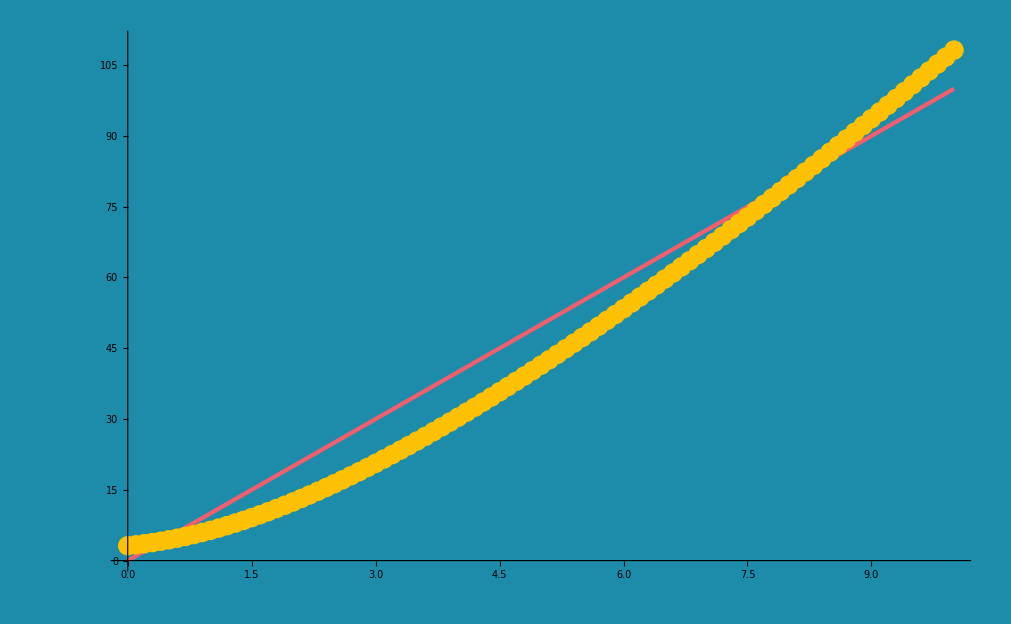

```mathematica
Show[Plot[10x, {x, 0, 10},PlotStyle->{RGBColor[0.949,0.367,0.427],Thickness[.003]}],ListPlot[b1, PlotStyle->RGBColor[0.998,0.754,0.006]], PlotRange->{{0,10},{0,110}}, BaseStyle->{FontSize->16},Background->RGBColor[0.110,0.549,0.667,1],AxesStyle->White,LabelStyle-> Large]
```

```mathematica
Show[%42,AxesLabel->{HoldForm[V1],HoldForm[V2]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
D[Log[Series[E^x^4,{x, 0, 100}]],x]
```

4 x^3+O[x]^100

```mathematica
D[density[x],x]
```

1.1 ⅇ^(x^1.1) x^0.1

```mathematica
Evaluate[Series[E^(x^(4)),{x, 0, 20}]]
```

1+x^4+x^8/2+x^12/6+x^16/24+x^20/120+O[x]^21

```mathematica
Evaluate[density[Abs[x]]]
```

1+Abs[x]^(3/2)+Abs[x]^3/2+1/6 Abs[x]^(9/2)+Abs[x]^6/24+1/120 Abs[x]^(15/2)+Abs[x]^9/720+Abs[x]^(21/2)/5040+Abs[x]^12/40320+Abs[x]^(27/2)/362880+Abs[x]^15/3628800+Abs[x]^(33/2)/39916800+Abs[x]^18/479001600+Abs[x]^(39/2)/6227020800

```mathematica
b1
```

{{0,2.43144},{0.1,2.55251},{0.2,2.67799},{0.3,2.80733},{0.4,2.94056},{0.5,3.07826},{0.6,3.22155},{0.7,3.37206},{0.8,3.53183},{0.9,3.70329},{1.,3.88905},{1.1,4.09181},{1.2,4.31413},{1.3,4.55832},{1.4,4.82623},{1.5,5.11926},{1.6,5.43827},{1.7,5.78364},{1.8,6.15535},{1.9,6.55302},{2.,6.97605},{2.1,7.42364},{2.2,7.89489},{2.3,8.38887},{2.4,8.90458},{2.5,9.44108},{2.6,9.99742},{2.7,10.5727},{2.8,11.1661},{2.9,11.7768},{3.,12.404},{3.1,13.047},{3.2,13.7052},{3.3,14.3779},{3.4,15.0645},{3.5,15.7646},{3.6,16.4775},{3.7,17.2029},{3.8,17.9402},{3.9,18.689},{4.,19.449},{4.1,20.2198},{4.2,21.001},{4.3,21.7923},{4.4,22.5934},{4.5,23.404},{4.6,24.2238},{4.7,25.0525},{4.8,25.8899},{4.9,26.7358},{5.,27.5899}}

```mathematica
b2
```

{{0,3.14655},{0.1,3.34311},{0.2,3.56641},{0.3,3.81758},{0.4,4.09748},{0.5,4.40673},{0.6,4.74568},{0.7,5.11445},{0.8,5.51294},{0.9,5.94091},{1.,6.39794},{1.1,6.88353},{1.2,7.39705},{1.3,7.93786},{1.4,8.50523},{1.5,9.09844},{1.6,9.71673},{1.7,10.3594},{1.8,11.0256},{1.9,11.7147},{2.,12.4259},{2.1,13.1586},{2.2,13.912},{2.3,14.6856},{2.4,15.4787},{2.5,16.2907},{2.6,17.1209},{2.7,17.969},{2.8,18.8343},{2.9,19.7163},{3.,20.6146},{3.1,21.5286},{3.2,22.4579},{3.3,23.4022},{3.4,24.3609},{3.5,25.3338},{3.6,26.3204},{3.7,27.3204},{3.8,28.3334},{3.9,29.3591},{4.,30.3972},{4.1,31.4474},{4.2,32.5094},{4.3,33.5829},{4.4,34.6676},{4.5,35.7634},{4.6,36.8699},{4.7,37.987},{4.8,39.1143},{4.9,40.2517},{5.,41.399}}

```mathematica
Evaluate[Normal[Series[E^(x^(6)),{x, 0, 150}]]]
```

1+x^6+x^12/2+x^18/6+x^24/24+x^30/120+x^36/720+x^42/5040+x^48/40320+x^54/362880+x^60/3628800+x^66/39916800+x^72/479001600+x^78/6227020800+x^84/87178291200+x^90/1307674368000+x^96/20922789888000+x^102/355687428096000+x^108/6402373705728000+x^114/121645100408832000+x^120/2432902008176640000+x^126/51090942171709440000+x^132/1124000727777607680000+x^138/25852016738884976640000+x^144/620448401733239439360000+x^150/15511210043330985984000000

-Graphics-